## 65.1 mA

```mathematica
files = FileNames["65.1mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

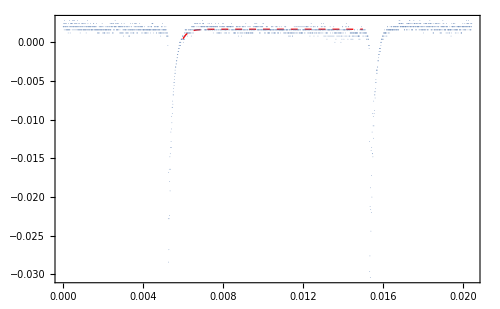
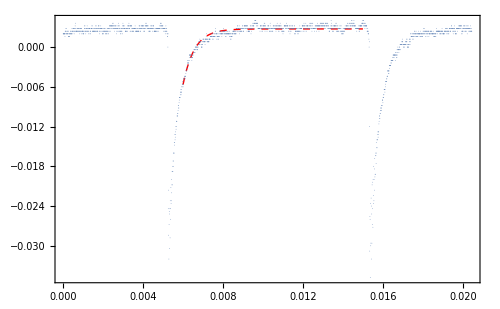
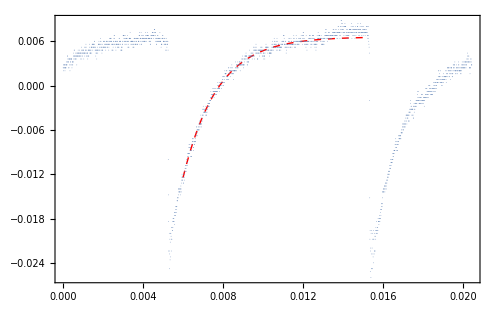
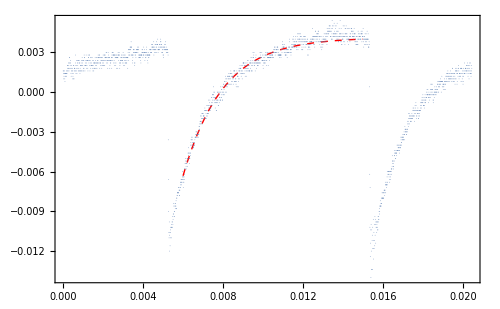
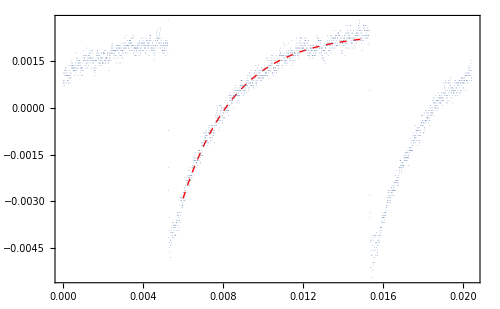
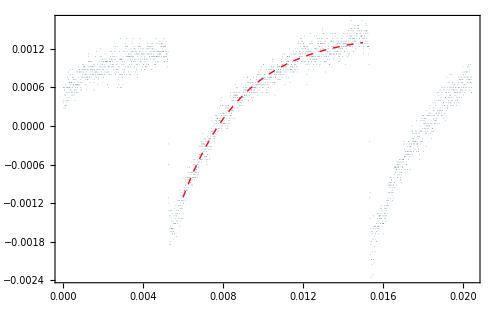
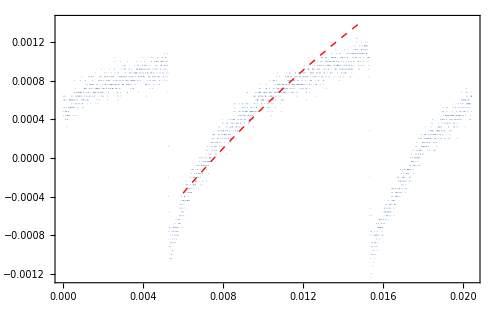
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{3917.28,1739.92,1739.92,578.57,499.253,373.717,325.832,45.8084}

{{1.,3917.28},{0.399268,1739.92},{0.351649,1739.92},{0.152625,578.57},{0.0891333,499.253},{0.0512826,373.717},{0.0317461,325.832}}

FittedModel[185.374+3794.8 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 185.374 | 69.2978 | 2.67504 | 0.0440814
b | 3794.8 | 159.705 | 23.7613 | 2.45895×10^-6

5.39449

2.0166

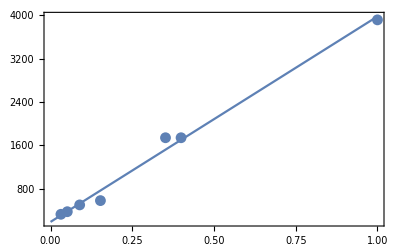

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, 0];
taudata = Drop[Transpose[{10^-filters, taus}],-1]

taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```

## 65.3 mA

```mathematica
files = FileNames["65.3mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

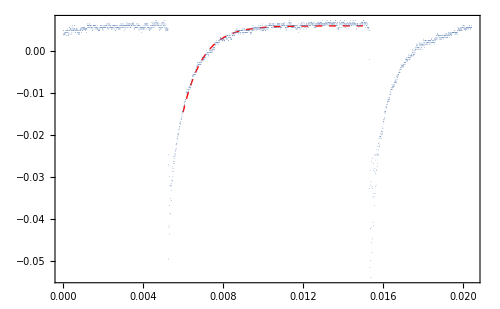
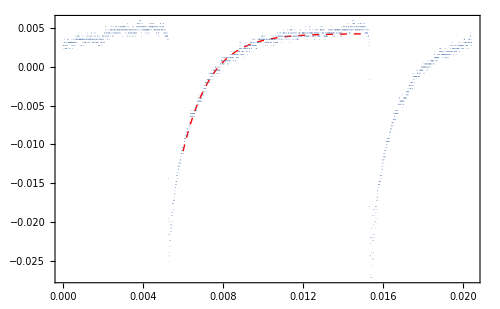
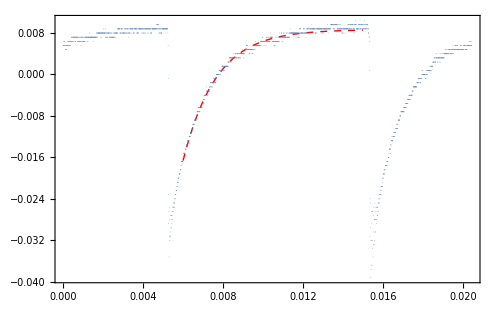
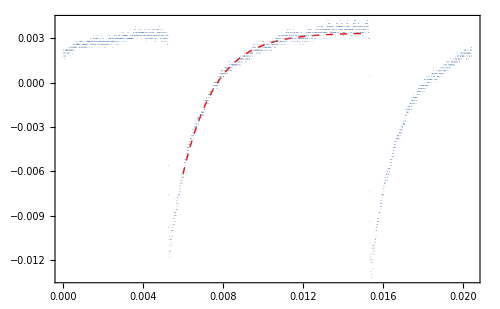
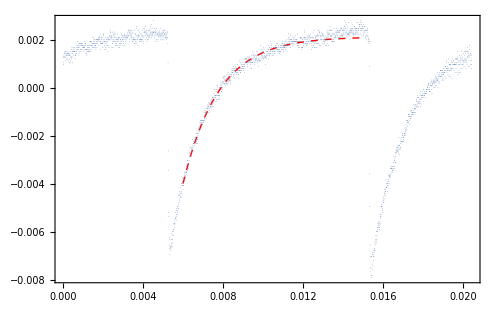
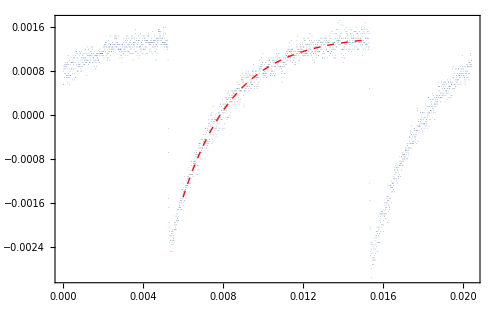
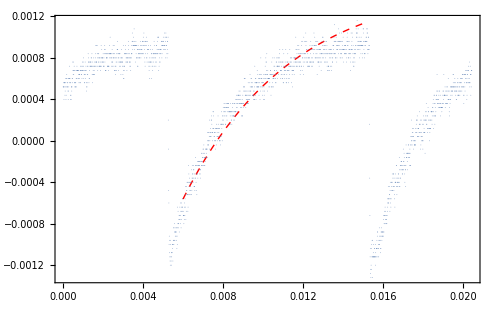
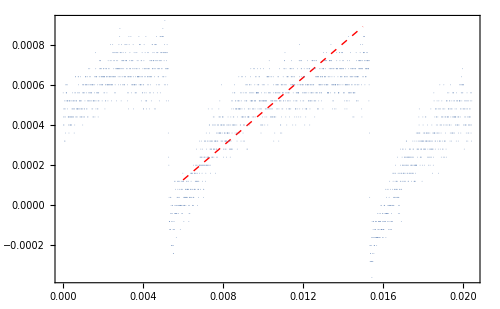

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{984.58,711.955,603.002,606.827,555.888,381.356,185.166,-0.37914}

{{1.,984.58},{0.399268,711.955},{0.351649,603.002},{0.152625,606.827},{0.0891333,555.888},{0.0512826,381.356}}

FittedModel[457.69+536.933 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 457.69 | 43.5187 | 10.5171 | 0.000462206
b | 536.933 | 92.8898 | 5.78033 | 0.0044494

2.18489

0.207746

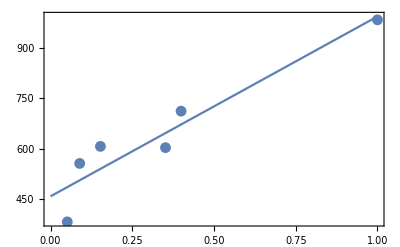

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, 0];

taudata = Drop[Transpose[{10^-filters, taus}],-2]
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```

## 65.5 mA

```mathematica
files = FileNames["65.5mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054&& #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#,{a - b ⅇ^(-c x)}, {{a,0.005}, {b,5}, {c,500}}, x]&/@fitdata;
#["ParameterTable"]&/@nlms
funcs = Normal[#]&/@ nlms;
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00522168 | 0.0000211919 | 246.4 | 8.9697800758×10^-726
b | 407155. | 28222.3 | 14.4267 | 7.23508×10^-42
c | 2907.72 | 12.4836 | 232.923 | 1.69263438848×10^-707, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00863352 | 0.0000269034 | 320.908 | 6.51880842095×10^-812
b | 92.2702 | 2.33752 | 39.4735 | 4.95666×10^-186
c | 1343.07 | 4.45361 | 301.569 | 1.30922636393×10^-791, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00979253 | 0.000028101 | 348.476 | 7.35724732993×10^-839
b | 33.67 | 0.65051 | 51.7593 | 4.98075×10^-251
c | 1145.25 | 3.37928 | 338.902 | 9.52448273992×10^-830, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00937069 | 0.0000294956 | 317.698 | 1.25806881755×10^-808
b | 2.13063 | 0.0260496 | 81.7915 | 2.39999741179×10^-378
c | 696.361 | 2.12985 | 326.952 | 5.19848097852×10^-818, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00768798 | 0.0000317872 | 241.858 | 1.0037817501×10^-719
b | 0.582456 | 0.0071414 | 81.5604 | 1.64679598097×10^-377
c | 534.244 | 2.17197 | 245.972 | 3.30307424524×10^-725, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00409912 | 0.0000212752 | 192.671 | 4.39365074333×10^-646
b | 0.127079 | 0.00151321 | 83.9802 | 3.5455363103×10^-386
c | 414.737 | 2.1969 | 188.782 | 1.65357457905×10^-639, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00225643 | 0.0000279761 | 80.6558 | 3.23085045521×10^-374
b | 0.0484389 | 0.0013221 | 36.6379 | 6.39494×10^-170
c | 376.383 | 5.16119 | 72.9257 | 7.76470784214×10^-345, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0013958 | 0.0000253702 | 55.0173 | 6.64306×10^-267
b | 0.0142394 | 0.000450871 | 31.582 | 2.28033×10^-140
c | 294.205 | 6.57783 | 44.7267 | 8.16955×10^-215}

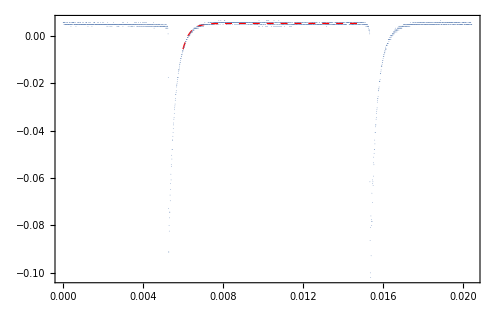
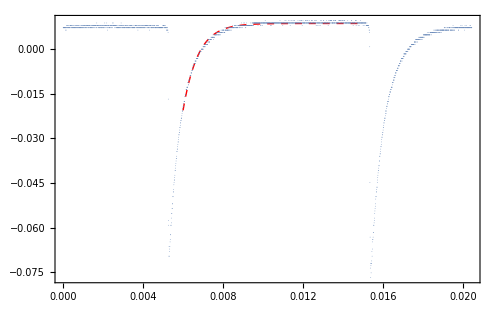
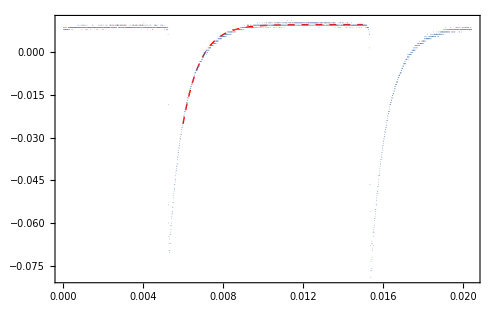
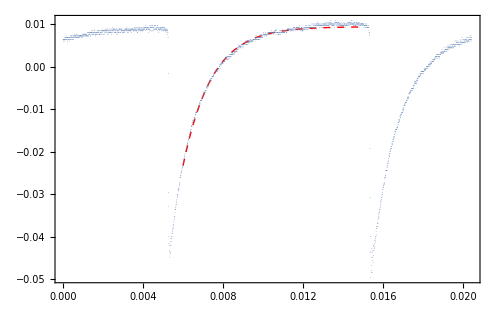
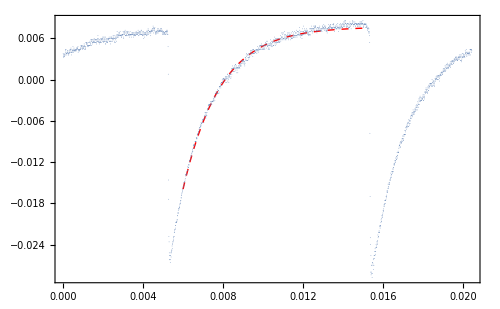
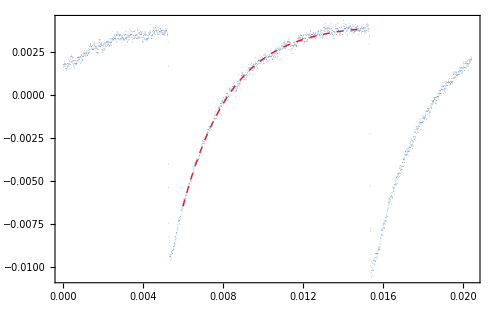
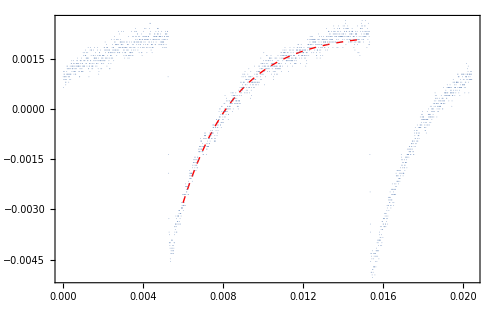
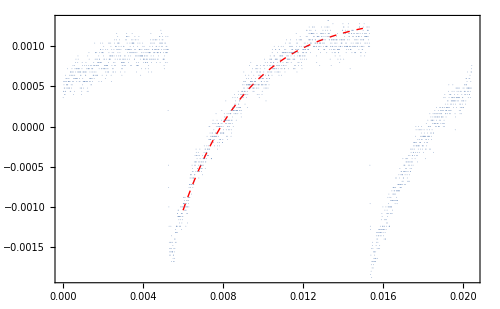

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

```mathematica
#["ParameterTableEntries"][[3, 1]]&/@nlms
#["ParameterTableEntries"][[3,2]]&/@nlms
```

{2907.72,1343.07,1145.25,696.361,534.244,414.737,376.383,294.205}

{12.4836,4.45361,3.37928,2.12985,2.17197,2.1969,5.16119,6.57783}

{2907.72,1343.07,1145.25,696.361,534.244,414.737,376.383,294.205}

{{1.,2907.72},{0.399268,1343.07},{0.351649,1145.25},{0.152625,696.361},{0.0891333,534.244},{0.0512826,414.737},{0.0317461,376.383},{0.0219781,294.205}}

{12.4836,4.45361,3.37928,2.12985,2.17197,2.1969,5.16119,6.57783}

FittedModel[293.031+2559.32 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 293.031 | 13.4436 | 21.797 | 6.08994×10^-7
b | 2559.32 | 68.3307 | 37.4549 | 2.41762×10^-8

3.4126

0.156563

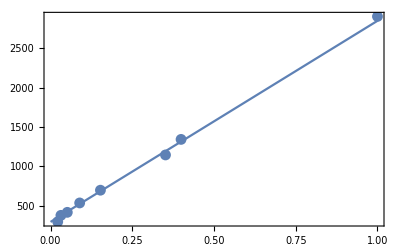

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = {0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801};
taudata = Transpose[{10^-filters, taus}]
tauserror=#["ParameterTableEntries"][[3,2]]&/@nlms
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x,Weights->1/tauserror^2]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```

## 65.7 mA

```mathematica
files = FileNames["65.7mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

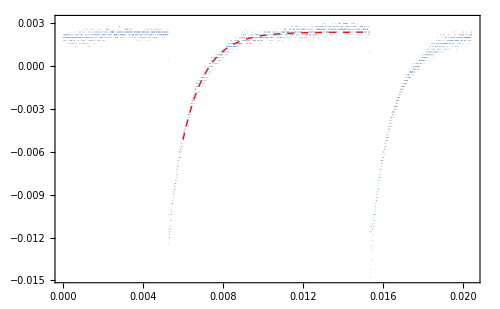
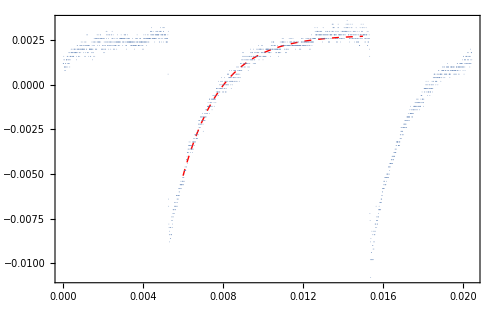
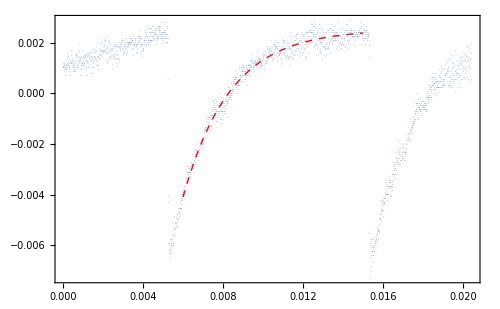
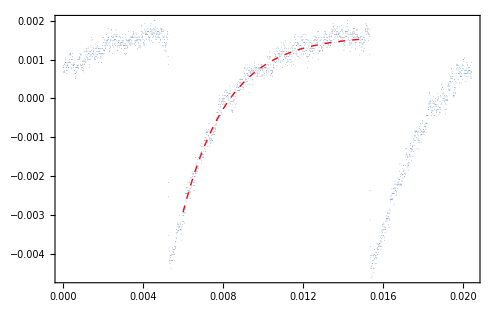
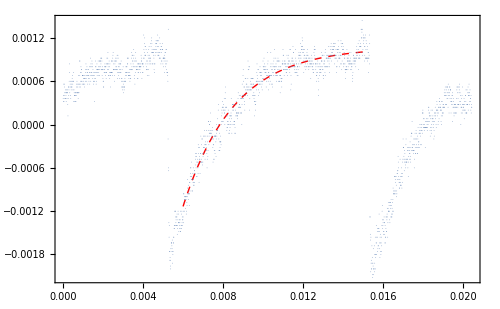
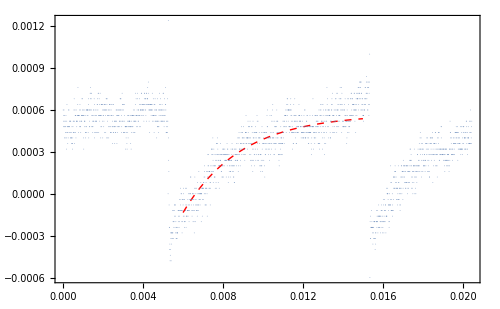

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{866.835,511.784,424.835,438.611,392.718,341.533}

{{1.,866.835},{0.399268,511.784},{0.351649,424.835},{0.152625,438.611},{0.0891333,392.718},{0.0512826,341.533}}

FittedModel[317.054+525.448 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 317.054 | 28.6664 | 11.0601 | 0.000380024
b | 525.448 | 61.188 | 8.58744 | 0.00101023

3.15404

0.285173

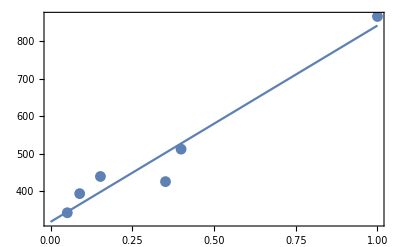

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, -2];
taudata = Transpose[{10^-filters, taus}]
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```